```mathematica
ClearAll[g,f,x,α,β];


beta[x_]:=(x)^(α-1)*(1-x)^(β-1)*(1/Beta[α,β])
(*Define the shifted Beta density on[-1,1]*)

g[y_]:=beta[(y+1)/2]

(*Define a scaled density on[-8,8] using the transformation y=x/8. The new density is f(x)=(1/8) g(x/8) to preserve normalization.*)
f[x_]:=g[x/8]

(*Plot the scaled density over the interval[-8,8]*)
Plot[f[x],{x,-8,8},AxesLabel->{"x","f(x)"},PlotLabel->"Scaled Shifted Beta Distribution (α = 3, β = 3) on [-8,8]"]
```

-Graphics-

```mathematica
xxx = FourierTransform[beta[x],x,Pb]
```

1/(√(2 π) Beta[α,β])(-((-1)^α Gamma[α] Gamma[1-α-β] HypergeometricPFQ[{1/2+α/2,α/2},{1/2,α/2+β/2,1/2+α/2+β/2},-Pb^2/4])/Gamma[1-β]-((-1)^β Gamma[1-α-β] Gamma[β] HypergeometricPFQ[{1/2+α/2,α/2},{1/2,α/2+β/2,1/2+α/2+β/2},-Pb^2/4])/Gamma[1-α]+(Gamma[α] Gamma[β] HypergeometricPFQ[{1/2+α/2,α/2},{1/2,α/2+β/2,1/2+α/2+β/2},-Pb^2/4])/Gamma[α+β]+Abs[Pb]^(-α-β) Gamma[-2+α+β] ((-1)^α Pb^2 (-1+β) Cos[1/2 π (α+β)] HypergeometricPFQ[{1-β/2,3/2-β/2},{3/2,3/2-α/2-β/2,2-α/2-β/2},-Pb^2/4]-(-1)^α (-2+α+β) Abs[Pb] HypergeometricPFQ[{1/2-β/2,1-β/2},{1/2,1-α/2-β/2,3/2-α/2-β/2},-Pb^2/4] Sin[1/2 π (α+β)]-(-1)^β (-1+β) Abs[Pb] (Abs[Pb] Cos[1/2 π (α+β)] HypergeometricPFQ[{1-β/2,3/2-β/2},{3/2,3/2-α/2-β/2,2-α/2-β/2},-Pb^2/4]+((-2+α+β) HypergeometricPFQ[{1/2-β/2,1-β/2},{1/2,1-α/2-β/2,3/2-α/2-β/2},-Pb^2/4] Sin[1/2 π (α+β)])/(-1+β)))+ⅈ Pb (((-1)^α Gamma[1+α] Gamma[-α-β] HypergeometricPFQ[{1/2+α/2,1+α/2},{3/2,1/2+α/2+β/2,1+α/2+β/2},-Pb^2/4])/Gamma[1-β]-((-1)^β Gamma[-α-β] Gamma[β] HypergeometricPFQ[{1/2+α/2,1+α/2},{3/2,1/2+α/2+β/2,1+α/2+β/2},-Pb^2/4])/Gamma[-α]+(Gamma[1+α] Gamma[β] HypergeometricPFQ[{1/2+α/2,1+α/2},{3/2,1/2+α/2+β/2,1+α/2+β/2},-Pb^2/4])/Gamma[1+α+β]+Abs[Pb]^(-α-β) Gamma[-2+α+β] (-(-1)^α (-2+α+β) Cos[1/2 π (α+β)] HypergeometricPFQ[{1/2-β/2,1-β/2},{1/2,1-α/2-β/2,3/2-α/2-β/2},-Pb^2/4]-(-1)^α (-1+β) Abs[Pb] HypergeometricPFQ[{1-β/2,3/2-β/2},{3/2,3/2-α/2-β/2,2-α/2-β/2},-Pb^2/4] Sin[1/2 π (α+β)]-(-1)^β (-1+β) (-1/(-1+β)(-2+α+β) Cos[1/2 π (α+β)] HypergeometricPFQ[{1/2-β/2,1-β/2},{1/2,1-α/2-β/2,3/2-α/2-β/2},-Pb^2/4]+Abs[Pb] HypergeometricPFQ[{1-β/2,3/2-β/2},{3/2,3/2-α/2-β/2,2-α/2-β/2},-Pb^2/4] Sin[1/2 π (α+β)]))))

```mathematica
α=1.333
β =3.5
```

1.333

3.5

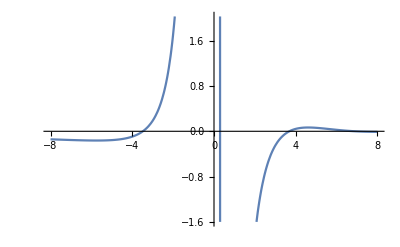

```mathematica
Plot[Re[xxx],{Pb,-8,8}]
```

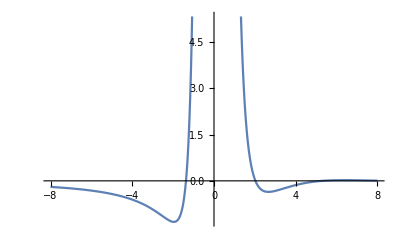

```mathematica
Plot[Im[xxx],{Pb,-8,8}]
```

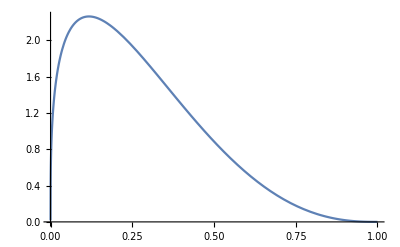

```mathematica
Plot[beta[x],{x,0,1}]
```